```mathematica
Needs["Quaternions`"];
quaternionToRotation[qq_]/;QuaternionQ[ToQuaternion[qq]]:=Module[{q=ToQuaternion[qq],aim,r},aim=AbsIJK[q];r=Re[q];
If[aim==0,Return[IdentityMatrix[3],Module]];
First[LinearAlgebra`Private`MatrixPolynomial[{Prepend[2 aim {r,aim}/(r^2+aim^2),1]},-LeviCivitaTensor[3,List].(Rest[List@@q]/aim)]]]
Needs["NumericalCalculus`"]
rotationToQuaternion[m_?OrthogonalMatrixQ]:=Module[{d,v,xm},d=Diagonal[m];
v={{m[[3,2]]-m[[2,3]],m[[1,3]]-m[[3,1]],m[[2,1]]-m[[1,2]]}};
xm=IdentityMatrix[4]+DiagonalMatrix[{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}}.d]+ArrayFlatten[{{0,v},{Transpose[v],2 Symmetrize[m-DiagonalMatrix[d]]}}];
Sign[Apply[Quaternion,First[MaximalBy[xm,Norm]]]]]

r=6600000; (*orbital radius, m*)
Subscript[μ, E]=3.986004418*10^14;
x[t_]:=({{q1[t]}, {q2[t]}, {q3[t]}, {q4[t]}, {w1[t]}, {w2[t]}, {w3[t]}});
i[t_] := ({{i1[t], 0, 0}, {0, i2[t], 0}, {0, 0, i3[t]}});

q[t_]:=Quaternion[q1[t],q2[t],q3[t],q4[t]];
rq[t_]:=Quaternion[0,Cos[θ[t]],Sin[θ[t]],0];
rtransform[t_]:=FullSimplify[Conjugate[q[t]]**rq[t]**q[t]][[2;;4]];
rb[t_]:={rtransform[t][[1]],rtransform[t][[2]],rtransform[t][[3]]};
M[t_] := 3 Subscript[μ, E]/r^3 FullSimplify[rb[t]×Flatten[i[t].rb[t]]];

w[t_]:={w1[t],w2[t],w3[t]};
qdot[t_] := 1/2({{0, -w1[t], -w2[t], -w3[t]}, {w1[t], 0, w3[t], -w2[t]}, {w2[t], -w3[t], 0, w1[t]}, {w3[t], w2[t], -w1[t], 0}}).({{q1[t]}, {q2[t]}, {q3[t]}, {q4[t]}});

wdot[t_]:= Inverse[i[t]].(((i[t].  w[t])×w[t])-(D[i[t], t]).w[t]);
eqns[t_] := ({{qdot[t][[1]][[1]]}, {qdot[t][[2]][[1]]}, {qdot[t][[3]][[1]]}, {qdot[t][[4]][[1]]}, {wdot[t][[1]]+M1[t]/i1[t]}, {wdot[t][[2]]+M2[t]/i2[t]}, {wdot[t][[3]]+M3[t]/i3[t]}});
rhs[t_]:= ({{q1'[t]}, {q2'[t]}, {q3'[t]}, {q4'[t]}, {w1'[t]}, {w2'[t]}, {w3'[t]}});
TraditionalForm[FullSimplify[rhs[t]==eqns[t]]]
```

(q1'(t)
q2'(t)
q3'(t)
q4'(t)
w1'(t)
w2'(t)
w3'(t))==(1/2 (-q2(t) w1(t)-q3(t) w2(t)-q4(t) w3(t))
1/2 (q1(t) w1(t)-q4(t) w2(t)+q3(t) w3(t))
1/2 (q4(t) w1(t)+q1(t) w2(t)-q2(t) w3(t))
1/2 (-q3(t) w1(t)+q2(t) w2(t)+q1(t) w3(t))
(M1(t)+(i2(t)-i3(t)) w2(t) w3(t)-w1(t) i1'(t))/(i1(t))
(M2(t)+(i3(t)-i1(t)) w1(t) w3(t)-w2(t) i2'(t))/(i2(t))
(M3(t)+(i1(t)-i2(t)) w1(t) w2(t)-w3(t) i3'(t))/(i3(t)))

```mathematica
range =100000;
R0 = EulerMatrix[{0°,0°,0°},{3,2,1}]; (*euler angles initial position, z-y-x intrinsic *)
quat0 = rotationToQuaternion[R0];
x0 = ({{quat0[[1]]}, {quat0 [[2]]}, {quat0 [[3]]}, {quat0 [[4]]}, {0}, {0}, {0}});   (*Initial conditions (q1,q2,q3,q4,w1,w2,w3)*)

system = NDSolve[{LogicalExpand[eqns[t]==rhs[t] && x[0]==x0 ],
θ[t]==√Subscript[μ, E]/r^3 t,
i1[t] ==0.1,
i2[t] ==10,
i3[t]==10,
M1[t]==M[t][[1]],
M2[t]==M[t][[2]],
M3[t]==M[t][[3]]
},
{q1,q2,q3,q4,w1,w2,w3},
{t,0,range},
PrecisionGoal->$MachinePrecision];

qq1= q1/.system[[1]];
qq2= q2/.system[[1]];
qq3= q3/.system[[1]];
qq4= q4/.system[[1]];
ww1=w1/.system[[1]];
ww2= w2/.system[[1]];
ww3= w3/.system[[1]];
qq1d= q1'/.system[[1]];
qq2d= q2'/.system[[1]];
qq3d= q3'/.system[[1]];
qq4d= q4'/.system[[1]];
ww1d=w1'/.system[[1]];
ww2d= w2'/.system[[1]];
ww3d= w3'/.system[[1]];
rotation[t_]:=quaternionToRotation[Quaternion[qq1[t],qq2[t],qq3[t],qq4[t]]];
angles[t_]:= EulerAngles[rotation[t],{3,2,1}];
psi[t_]:= angles[t][[1]];
alpha[t_]:= angles[t][[2]];
gamma[t_]:= angles[t][[3]];
newrot[t_]:=rotation[t].{Cos[theta[t]],-Sin[theta[t]],0}
psii[t_]:= ArcTan[ newrot[t][[2]]/newrot[t][[1]]]
T = 2 Pi /√Subscript[μ, E]/r^3
Plot[psii[t],{t,0,2T}]


(*Inertial Frame*)
oneaxis[t_] := {Blue, Line[{{0,0,0},{rotation[t].{1,0,0}}[[1]]}]};
twoaxis[t_] := {Red, Line[{{0,0,0},{rotation[t].{0,1,0}}[[1]]}]};
threeaxis[t_] := {Green, Line[{{0,0,0},{rotation[t].{0,0,1}}[[1]]}]};
trange = 500;
trace1[t_]:= {Blue, Line[{Table[{rotation[n].{1,0,0}}[[1]],{n,If[t>trange,t-trange,0],t,0.1}]}]};
trace2[t_]:= {Red, Line[{Table[{rotation[n].{0,1,0}}[[1]],{n,If[t>trange,t-trange,0],t,0.1}]}]};
trace3[t_]:= {Green, Line[{Table[{rotation[n].{0,0,1}}[[1]],{n,If[t>trange,t-trange,0],t,0.1}]}]};
scene[t_]:={oneaxis[t],twoaxis[t],threeaxis[t]};
inertial[t_]:=Graphics3D[scene[t],PlotRange->1,ImageSize->Medium];


(*Body Centred Rotating Frame*)
theta[t_]=√Subscript[μ, E]/r^3 t;
oneaxis2[t_] := {Blue, Line[{{0,0,0},{rotation[t].{Cos[theta[t]],-Sin[theta[t]],0}}[[1]]}]};
twoaxis2[t_] := {Red, Line[{{0,0,0},{rotation[t].{Sin[theta[t]],Cos[theta[t]],0}}[[1]]}]};
threeaxis2[t_] := {Green, Line[{{0,0,0},{rotation[t].{0,0,1}}[[1]]}]};
nadir[t_]:={Black,Thick,Line[{{0,0,0},{-1,0,0}}]};
scene2[t_]:={oneaxis2[t],twoaxis2[t],threeaxis2[t],nadir[t]};
bodycentred[t_]:=Graphics3D[scene2[t],PlotRange->1,ImageSize->Medium];


(*Earth Centred Inertial*)
rcc[t_]:=r{Cos[theta[t]],Sin[theta[t]],0};
rc[t_]:={Black,Thick,Line[{{0,0,0},rcc[t]}]};
oneaxis3[t_] := {Blue, Line[{rcc[t],rcc[t]+r/5{rotation[t].{1,0,0}}[[1]]}]};
twoaxis3[t_] := {Red, Line[{rcc[t],rcc[t]+r/5{rotation[t].{0,1,0}}[[1]]}]};
threeaxis3[t_] := {Green, Line[{rcc[t],rcc[t]+r/5{rotation[t].{0,0,1}}[[1]]}]};
scene3[t_]:={rc[t],oneaxis3[t],twoaxis3[t],threeaxis3[t]};
earthcentred[t_]:=Graphics3D[scene3[t],PlotRange->1.2r,ImageSize->Medium];
Manipulate[Grid[{{inertial[t],bodycentred[t],earthcentred[t]}},Spacings->0],{t,0,range,Appearance-> "Open", AnimationRate->120,RefreshRate->60,AnimationRunning->True}]
(*Body centred inertial frame, body centred rotating frame, earth centred inertial frame*)
```

```mathematica
Manipulate[ParametricPlot[{psi[t],ww3[t]},{t,0,n},AspectRatio->Full,PlotRange->All],{n,1,2T,T}]
```

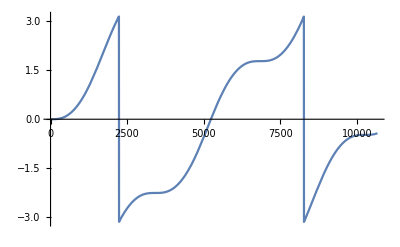

```mathematica
Plot[psi[t],{t,0,2T}]
Manipulate[ListLinePlot[{{0,0},newrot[t][[1;;2]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,FrameTicks->True],{t,0,2T}]
```

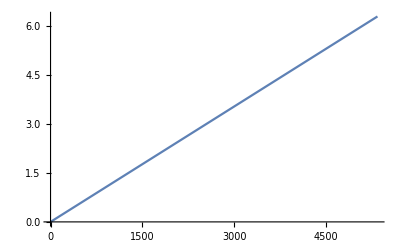

5336.14

```mathematica
Plot[SawtoothWave[{0,2Pi},(√Subscript[μ, E]/r^3/(2 Pi))t],{t,0,T}]
```

```mathematica
newrot[t_]:=rotation[t].{Cos[theta[t]],-Sin[theta[t]],0}
psii[t_]:= ArcTan[ newrot[t][[2]]/newrot[t][[1]]]
```

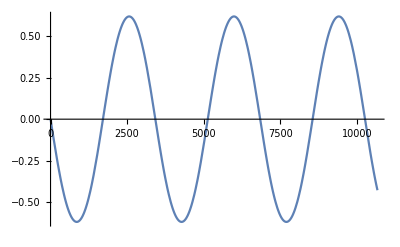

```mathematica
Plot[psii[t],{t,0,2T}]
```